```mathematica
FullSimplify@Sum[Pochhammer[z,j]/j!,{j,0,n}]
```

Gamma[1+n+z]/(Gamma[1+n] Gamma[1+z])

```mathematica
FullSimplify@Sum[j/j!,{j,1,n}]
```

(-1+ⅇ Gamma[1+n,1])/Gamma[1+n]

```mathematica
FullSimplify@Sum[j^2/j!,{j,1,n}]
```

-(2+n-2 ⅇ Gamma[1+n,1])/Gamma[1+n]

```mathematica
FullSimplify@Sum[j^3/j!,{j,1,n}]
```

(-5-n (3+n)+5 ⅇ Gamma[1+n,1])/Gamma[1+n]

```mathematica
Sum[z^j/j!,{j,1,n}]
```

-1+(ⅇ^z Gamma[1+n,z])/Gamma[1+n]

```mathematica
Pochhammer[z,3]
```

z (1+z) (2+z)

```mathematica
Expand@z^3
```

z^3

```mathematica
Sum[Binomial[z,k] FactorialPower[x,k]/k!,{k,0,Infinity}]
```

Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])

```mathematica
FactorialPower[x-1,k-1]/(k-1)!/.x->18/.k->5
```

2380

```mathematica
Binomial[18-1,5-1]
```

2380

```mathematica
Binomial[18,5]-Binomial[17,5]
```

2380

```mathematica
Clear[d2]
d2[n_,k_]:=d2[n,k]=Sum[d2[Floor[n/j],k-1],{j,2,n}]
d2[n_,0]:=UnitStep[n-1]
dd2[n_,k_]:=d2[n,k]-d2[n-1,k]
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,s_,z_]:=n^-s Product[(-1)^p[[2]]Binomial[-z,p[[2]]],{p,FI[n]}]
dz2[n_,k_]:=Sum[(-1)^(k-j) Binomial[k,j]dz[n,0,j],{j,0,k}]
```

```mathematica
Table[dd2[2^n,2],{n,1,8}]
```

{0,1,2,3,4,5,6,7}

```mathematica
Table[dd2[30^n,2],{n,1,4}]
```

{6,25,62,123}

```mathematica
Table[(n+1)^3-2,{n,1,4}]
```

{6,25,62,123}

```mathematica
Table[dd2[2^n,3],{n,1,8}]
```

{0,0,1,3,6,10,15,21}

```mathematica
Table[Pochhammer[n-2,2]/2!,{n,1,8}]
```

{0,0,1,3,6,10,15,21}

```mathematica
Table[dd2[2^n,4],{n,1,8}]
```

{0,0,0,1,4,10,20,35}

```mathematica
Table[Pochhammer[n-3,3]/3!,{n,1,8}]
```

{0,0,0,1,4,10,20,35}

```mathematica
Table[Pochhammer[n-1,1]/1!,{n,1,8}]
```

{0,1,2,3,4,5,6,7}

```mathematica
d2a[a_,k_]:=Pochhammer[a-(k-1),(k-1)]/(k-1)!
```

```mathematica
dd2[2^8,5]
```

35

```mathematica
d2a[8,5]
```

35

```mathematica
FullSimplify[Pochhammer[a-(k-1),(k-1)]/(k-1)!]
```

Gamma[a]/(Gamma[1+a-k] Gamma[k])

```mathematica
dd2[6,3]
```

0

```mathematica
d2b[1,1,2]
```

0

```mathematica
Grid@Table[dz2[6^n,k],{k,1,9},{n,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 7 | 14 | 23 | 34 | 47 | 62 | 79
0 | 12 | 55 | 153 | 336 | 640 | 1107 | 1785
0 | 6 | 92 | 471 | 1584 | 4210 | 9596 | 19607
0 | 0 | 70 | 780 | 4251 | 16175 | 49225 | 128345
0 | 0 | 20 | 720 | 7002 | 39733 | 164898 | 555303
0 | 0 | 0 | 350 | 7238 | 65226 | 380731 | 1685257
0 | 0 | 0 | 70 | 4592 | 72660 | 623576 | 3716695
0 | 0 | 0 | 0 | 1638 | 54390 | 732618 | 6077196

```mathematica
Grid@Table[dz2[3 2^n,k],{k,1,9},{n,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0 | 3 | 9 | 18 | 30 | 45 | 63 | 84
0 | 0 | 4 | 16 | 40 | 80 | 140 | 224
0 | 0 | 0 | 5 | 25 | 75 | 175 | 350
0 | 0 | 0 | 0 | 6 | 36 | 126 | 336
0 | 0 | 0 | 0 | 0 | 7 | 49 | 196
0 | 0 | 0 | 0 | 0 | 0 | 8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9

```mathematica
Grid@Table[dz2[3 2^n,k],{k,1,9},{n,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0 | 3 | 9 | 18 | 30 | 45 | 63 | 84
0 | 0 | 4 | 16 | 40 | 80 | 140 | 224
0 | 0 | 0 | 5 | 25 | 75 | 175 | 350
0 | 0 | 0 | 0 | 6 | 36 | 126 | 336
0 | 0 | 0 | 0 | 0 | 7 | 49 | 196
0 | 0 | 0 | 0 | 0 | 0 | 8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9

```mathematica
Grid@Table[k Binomial[a,k-1],{k,1,9},{a,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16
0 | 3 | 9 | 18 | 30 | 45 | 63 | 84
0 | 0 | 4 | 16 | 40 | 80 | 140 | 224
0 | 0 | 0 | 5 | 25 | 75 | 175 | 350
0 | 0 | 0 | 0 | 6 | 36 | 126 | 336
0 | 0 | 0 | 0 | 0 | 7 | 49 | 196
0 | 0 | 0 | 0 | 0 | 0 | 8 | 64
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9

```mathematica
Grid@Table[dz2[3^2 2^n,k],{k,1,9},{n,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 7 | 10 | 13 | 16 | 19 | 22 | 25
3 | 12 | 27 | 48 | 75 | 108 | 147 | 192
0 | 6 | 28 | 76 | 160 | 290 | 476 | 728
0 | 0 | 10 | 55 | 175 | 425 | 875 | 1610
0 | 0 | 0 | 15 | 96 | 351 | 966 | 2226
0 | 0 | 0 | 0 | 21 | 154 | 637 | 1960
0 | 0 | 0 | 0 | 0 | 28 | 232 | 1072
0 | 0 | 0 | 0 | 0 | 0 | 36 | 333

```mathematica
Grid@Table[  dz2[3 5 2^n,k],{k,1,9},{n,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 10 | 14 | 18 | 22 | 26 | 30 | 34
6 | 21 | 45 | 78 | 120 | 171 | 231 | 300
0 | 12 | 52 | 136 | 280 | 500 | 812 | 1232
0 | 0 | 20 | 105 | 325 | 775 | 1575 | 2870
0 | 0 | 0 | 30 | 186 | 666 | 1806 | 4116
0 | 0 | 0 | 0 | 42 | 301 | 1225 | 3724
0 | 0 | 0 | 0 | 0 | 56 | 456 | 2080
0 | 0 | 0 | 0 | 0 | 0 | 72 | 657

```mathematica
Grid@Table[(k n+1)k Binomial[n+1,k-1]/(n+1),{k,1,9},{n,1,8}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 10 | 14 | 18 | 22 | 26 | 30 | 34
6 | 21 | 45 | 78 | 120 | 171 | 231 | 300
0 | 12 | 52 | 136 | 280 | 500 | 812 | 1232
0 | 0 | 20 | 105 | 325 | 775 | 1575 | 2870
0 | 0 | 0 | 30 | 186 | 666 | 1806 | 4116
0 | 0 | 0 | 0 | 42 | 301 | 1225 | 3724
0 | 0 | 0 | 0 | 0 | 56 | 456 | 2080
0 | 0 | 0 | 0 | 0 | 0 | 72 | 657

```mathematica
(k n+1)k Binomial[n+1,k-1]/(n+1)
```

(k (1+k n) Binomial[1+n,-1+k])/(1+n)

```mathematica
(k n+1)k /(n+1)
```

(k (1+k n))/(1+n)

```mathematica
(k n+1)k Binomial[n+1,k-1]/(n+1)/.n->a
```

(k (1+a k) Binomial[1+a,-1+k])/(1+a)

```mathematica
Grid@Table[dz2[3^2 2^n,k],{k,1,7},{n,1,10}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 7 | 10 | 13 | 16 | 19 | 22 | 25 | 28 | 31
3 | 12 | 27 | 48 | 75 | 108 | 147 | 192 | 243 | 300
0 | 6 | 28 | 76 | 160 | 290 | 476 | 728 | 1056 | 1470
0 | 0 | 10 | 55 | 175 | 425 | 875 | 1610 | 2730 | 4350
0 | 0 | 0 | 15 | 96 | 351 | 966 | 2226 | 4536 | 8442
0 | 0 | 0 | 0 | 21 | 154 | 637 | 1960 | 4998 | 11172

```mathematica
Grid@Table[(n k(k+1)/2-k(k-3)/2)(Binomial[n+1,k-1]/(n+1)),{k,1,7},{n,1,10}]
```

1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 7 | 10 | 13 | 16 | 19 | 22 | 25 | 28 | 31
3 | 12 | 27 | 48 | 75 | 108 | 147 | 192 | 243 | 300
0 | 6 | 28 | 76 | 160 | 290 | 476 | 728 | 1056 | 1470
0 | 0 | 10 | 55 | 175 | 425 | 875 | 1610 | 2730 | 4350
0 | 0 | 0 | 15 | 96 | 351 | 966 | 2226 | 4536 | 8442
0 | 0 | 0 | 0 | 21 | 154 | 637 | 1960 | 4998 | 11172

```mathematica
FullSimplify@Expand[(n k(k+1)/2-k(k-3)/2)(Binomial[n+1,k-1]/(n+1))]/.n->a
```

(k (3+a+(-1+a) k) Binomial[1+a,-1+k])/(2 (1+a))

```mathematica
FullSimplify[(k (3+a+(-1+a) k) Binomial[1+a,-1+k])/(2 (1+a))/.a->2]
```

```mathematica
FullSimplify@Expand[(k (1+a k) Binomial[1+a,-1+k])/(1+a)/.a->1]
```

1/2 k (1+k) Binomial[2,-1+k]

```mathematica
Table[k (1+k)/2 Binomial[2,k-1],{k,0,5}]
```

{0,1,6,6,0,0}

```mathematica
Binomial[ k+1,k-1]
```

1/2 k (1+k)

```mathematica
Table[Binomial[k,k-1],{k,0,5}]
```

{0,1,2,3,4,5}

```mathematica
FullSimplify[Binomial[z,k] (z+1)/(z-k)]
```

((1+z) Binomial[z,k])/(-k+z)

```mathematica
Table[k Binomial[1,k-1],{k,0,5}]
```

{0,1,2,0,0,0}

```mathematica
Table[(k)(3-k)/2,{k,1,6}]
```

{1,1,0,-2,-5,-9}

```mathematica
(k (3+a+(-1+a) k) Binomial[1+a,-1+k])/(2 (1+a))/.a->2
```

```mathematica
Table[1/6 k (5+k) Binomial[3,-1+k],{k,0,5}]
```

{0,1,7,12,6,0}

```mathematica
Table[dz2[6^2,j],{j,0,5}]
```

{0,1,7,12,6,0}

```mathematica
Table[1/6 k (5+k) FactorialPower[3,-1+k]/(k-1)!,{k,0,5}]
```

{0,1,7,12,6,0}

```mathematica
FullSimplify[1/6 k (5+k) FactorialPower[3,-1+k]/(k-1)!]
```

(k (5+k) FactorialPower[3,-1+k])/(6 Gamma[k])

```mathematica
FactorialPower[3,-1+k]
```

FactorialPower[3,-1+k]

```mathematica
Table[FactorialPower[3,-1+k],{k,0,5}]
```

{1/4,1,3,6,6,0}

```mathematica
binx[z_,k_]:=Binomial[z,k]
bin[z_,k_]:=Gamma[z+1]/Gamma[z-k+1]/Gamma[k+1]
da[a_,k_]:=bin[a-1,k-1]
da1[a_,k_]:=k bin[a,k-1]
da11[a_,k_]:=k (1+a k)/(1+a) bin[a+1,k-1]
da2[a_,k_]:=k ((3+a+(a-1)k)/(2(a+1)))bin[a+1,k-1]
d2f[z_]:=da[1,z]+da[1,z]+da[2,z]+da[1,z]+da1[1,z]+da[1,z]+da[3,z]+da[2,z]+da1[1,z]
d2f2[z_]:=d2f[z]+da[1,z]+da1[2,z]+da[1,z]+da1[1,z]+da1[1,z]+da[4,z]+da[1,z]+da1[2,z]+da[1,z]+da1[2,z]
d2f3[z_]:=d2f2[z]+da1[1,z]+da1[1,z]+da[1,z]+da1[3,z]+da[2,z]+da1[1,z]+da[3,z]+da1[2,z]+da[1,z]+da11[1,z]
Clear[v]
v[z_,1]:=0 
v[z_,2]:=v[z,1]+da[1,z]
v[z_,3]:=v[z,2]+da[1,z]
v[z_,4]:=v[z,3]+da[2,z]
v[z_,5]:=v[z,4]+da[1,z]
v[z_,6]:=v[z,5]+da1[1,z]
v[z_,7]:=v[z,6]+da[1,z]
v[z_,8]:=v[z,7]+da[3,z]
v[z_,9]:=v[z,8]+da[2,z]
v[z_,10]:=v[z,10]=v[z,9]+da1[1,z]
v[z_,11]:=v[z,10]+da[1,z]
v[z_,12]:=v[z,11]+da1[2,z]
v[z_,13]:=v[z,12]+da[1,z]
v[z_,14]:=v[z,13]+da1[1,z]
v[z_,15]:=v[z,14]+da1[1,z]
v[z_,16]:=v[z,15]+da[4,z]
v[z_,17]:=v[z,16]+da[1,z]
v[z_,18]:=v[z,17]+da1[2,z]
v[z_,19]:=v[z,18]+da[1,z]
v[z_,20]:=v[z,20]=v[z,19]+da1[2,z]
v[z_,21]:=v[z,20]+da1[1,z]
v[z_,22]:=v[z,21]+da1[1,z]
v[z_,23]:=v[z,22]+da[1,z]
v[z_,24]:=v[z,23]+da1[3,z]
v[z_,25]:=v[z,24]+da[2,z]
v[z_,26]:=v[z,25]+da1[1,z]
v[z_,27]:=v[z,26]+da[3,z]
v[z_,28]:=v[z,27]+da1[2,z]
v[z_,29]:=v[z,28]+da[1,z]
v[z_,30]:=v[z,30]=v[z,29]+da11[1,z]
v[z_,31]:=v[z,30]+da[1,z]
v[z_,32]:=v[z,31]+da[5,z]
v[z_,33]:=v[z,32]+da1[1,z]
v[z_,34]:=v[z,33]+da1[1,z]
v[z_,35]:=v[z,34]+da1[1,z]
v[z_,36]:=v[z,35]+da2[2,z]
v[z_,37]:=v[z,36]+da[1,z]
v[z_,38]:=v[z,37]+da1[1,z]
v[z_,39]:=v[z,38]+da1[1,z]
v[z_,40]:=v[z,40]=v[z,39]+da1[3,z]
v[z_,41]:=v[z,40]+da[1,z] 
v[z_,42]:=v[z,41]+da11[1,z]
v[z_,43]:=v[z,42]+da[1,z]
v[z_,44]:=v[z,43]+da1[2,z]
v[z_,45]:=v[z,44]+da1[2,z]
v[z_,46]:=v[z,45]+da1[1,z]
v[z_,47]:=v[z,46]+da[1,z]
v[z_,48]:=v[z,47]+da1[4,z]
v[z_,49]:=v[z,48]+da[2,z]
v[z_,50]:=v[z,50]=v[z,49]+da1[2,z]
v[z_,51]:=v[z,50]+da1[1,z]
v[z_,52]:=v[z,51]+da1[2,z]
v[z_,53]:=v[z,52]+da[1,z]
v[z_,54]:=v[z,53]+da1[3,z]
v[z_,55]:=v[z,54]+da1[1,z]
v[z_,56]:=v[z,55]+da1[3,z]
v[z_,57]:=v[z,56]+da1[1,z]
v[z_,58]:=v[z,57]+da1[1,z]
v[z_,59]:=v[z,58]+da[1,z]
v[z_,60]:=v[z,60]=v[z,59]+da11[2,z]
v[z_,61]:=v[z,60]+da[1,z]
v[z_,62]:=v[z,61]+da1[1,z]
v[z_,63]:=v[z,62]+da1[2,z]
v[z_,64]:=v[z,63]+da[6,z]
v[z_,65]:=v[z,64]+da1[1,z]
v[z_,66]:=v[z,65]+da11[1,z]
v[z_,67]:=v[z,66]+da[1,z]
v[z_,68]:=v[z,67]+da1[2,z]
v[z_,69]:=v[z,68]+da1[1,z]
v[z_,70]:=v[z,70]=v[z,69]+da11[1,z]
```

```mathematica
Table[FactorInteger[k],{k,61,70}]
```

{{{61,1}},{{2,1},{31,1}},{{3,2},{7,1}},{{2,6}},{{5,1},{13,1}},{{2,1},{3,1},{11,1}},{{67,1}},{{2,2},{17,1}},{{3,1},{23,1}},{{2,1},{5,1},{7,1}}}

```mathematica
{Limit[D[FullSimplify@v[z,70],z],z->0],Sum[FullSimplify[MangoldtLambda[j]/Log[j]],{j,2,70}]}
```

{1337/60,1337/60}

```mathematica
Table[d2[30,k],{k,1,6}]
```

{29,52,32,5,0,0}

```mathematica
Table[d2f3[k],{k,1,6}]
```

{29,52,32,5,0,0}

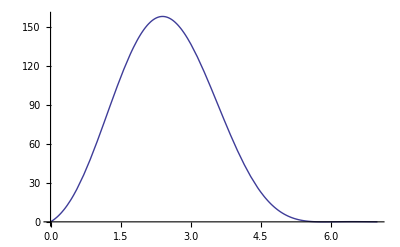

```mathematica
Plot[v[x,63],{x,0,7}]
```

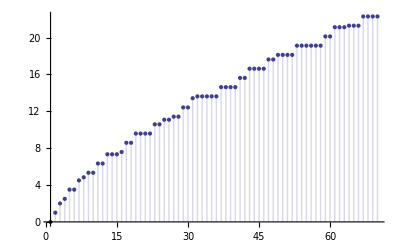

```mathematica
DiscretePlot[Limit[D[v[z,n],z],z->0],{n,1,70}]
```

```mathematica
Sum[FullSimplify[MangoldtLambda[j]/Log[j]],{j,2,35}]
```

817/60

```mathematica
FullSimplify@d2f3[z]
```

((298+z (-159+(39-4 z) z)) Sin[π z])/(π (-4+z) (-3+z) (-2+z) (-1+z))

```mathematica
Expand@((298+z (-159+(39-4 z) z))/((-4+z) (-3+z) (-2+z) (-1+z)))
```

298/((-4+z) (-3+z) (-2+z) (-1+z))-(159 z)/((-4+z) (-3+z) (-2+z) (-1+z))+(39 z^2)/((-4+z) (-3+z) (-2+z) (-1+z))-(4 z^3)/((-4+z) (-3+z) (-2+z) (-1+z))

```mathematica
d2[30,5]
```

0

```mathematica
Limit[D[(298+z (-159+(39-4 z) z))/((-4+z) (-3+z) (-2+z) (-1+z)),z],z->0]
```

2771/144

```mathematica
Limit[D[((298+z (-159+(39-4 z) z)) Sin[π z])/(π (-4+z) (-3+z) (-2+z) (-1+z)),z],z->0]
```

149/12

```mathematica
Expand[(298+z (-159+(39-4 z) z))]
```

298-159 z+39 z^2-4 z^3

```mathematica
d2f3[z]
```

```mathematica
Table[FullSimplify@Limit[D[d2f3[z],{z,k}],z->0],{k,0,5}]
```

Limit::ztest1: Unable to decide whether numeric quantity -35245/10368 - 145/12\ PolyGamma[2, 2] + 15/2\ PolyGamma[2, 3] + 10/3\ PolyGamma[2, 4] + 5/4\ PolyGamma[2, 5] is equal to zero. Assuming it is.

{0,149/12,2771/72,1/288 (40793-3576 π^2),17/864 (31867-3912 π^2),(34216645-4895160 π^2+128736 π^4)/10368}

```mathematica
d2f3[z]
```

10 Binomial[0,-1+z]+3 Binomial[1,-1+z]+7 z Binomial[1,-1+z]+2 Binomial[2,-1+z]+4 z Binomial[2,-1+z]+1/2 z (1+z) Binomial[2,-1+z]+Binomial[3,-1+z]+z Binomial[3,-1+z]

```mathematica
FullSimplify@d2f[z]
```

4 Binomial[0,-1+z]+2 (1+z) Binomial[1,-1+z]+Binomial[2,-1+z]

```mathematica
Table[Expand@FullSimplify@v[z,n],{n,15,17}]
```

{44/(Gamma[4-z] Gamma[z])-(18 z)/(Gamma[4-z] Gamma[z])+(2 z^2)/(Gamma[4-z] Gamma[z]),182/(Gamma[5-z] Gamma[z])-(116 z)/(Gamma[5-z] Gamma[z])+(26 z^2)/(Gamma[5-z] Gamma[z])-(2 z^3)/(Gamma[5-z] Gamma[z]),(206 Sin[π z])/(π (-4+z) (-3+z) (-2+z) (-1+z))-(142 z Sin[π z])/(π (-4+z) (-3+z) (-2+z) (-1+z))+(35 z^2 Sin[π z])/(π (-4+z) (-3+z) (-2+z) (-1+z))-(3 z^3 Sin[π z])/(π (-4+z) (-3+z) (-2+z) (-1+z))}

```mathematica
Table[d2[50,k],{k,0,6}]
```

{1,49,108,92,35,6,0}

```mathematica
Table[v[k,50],{k,0,6}]
```

{0,49,108,92,35,6,0}

```mathematica
Grid@Table[d2[n,k],{n,1,10},{k,1,6}]
```

0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 0 | 0
3 | 1 | 0 | 0 | 0 | 0
4 | 1 | 0 | 0 | 0 | 0
5 | 3 | 0 | 0 | 0 | 0
6 | 3 | 0 | 0 | 0 | 0
7 | 5 | 1 | 0 | 0 | 0
8 | 6 | 1 | 0 | 0 | 0
9 | 8 | 1 | 0 | 0 | 0

```mathematica
Solve[{ c1- c2== v1,
c1-2c2==v2},
{c1,c2}]/.v1->D1/.v2->D2/.v3->D3/.v4->D4/.v5->D5/.v6->D6
```

{{c1→2 D1-D2,c2→D1-D2}}

```mathematica
Solve[{ c1- c2+c3==2 v1,
c1-2c2+4c3==v2, 
c1-3c2+9c3==2 v3},
{c1,c2,c3}]/.v1->D1/.v2->D2/.v3->D3/.v4->D4/.v5->D5/.v6->D6
```

{{c1→6 D1-3 D2+2 D3,c2→5 D1-4 D2+3 D3,c3→D1-D2+D3}}

```mathematica
Expand@Solve[{ c1- c2+c3-c4==6v1,
c1-2c2+4c3-8 c4==2v2,
 c1-3c2+9c3-27 c4==2v3,
 c1-4c2+16c3-64 c4==6v4},
{c1,c2,c3,c4}]/.v1->D1/.v2->D2/.v3->D3/.v4->D4/.v5->D5/.v6->D6
```

{{c1→24 D1-12 D2+8 D3-6 D4,c2→26 D1-19 D2+14 D3-11 D4,c3→9 D1-8 D2+7 D3-6 D4,c4→D1-D2+D3-D4}}

```mathematica
Expand@Solve[{ c1- c2+c3-c4+c5==24v1,
c1-2c2+4c3-8 c4+16 c5==6v2,
 c1-3c2+9c3-27 c4+81 c5==4v3,
 c1-4c2+16c3-64 c4+256 c5==6v4,
c1-5c2+25c3-125 c4+625 c5==24v5},
{c1,c2,c3,c4,c5}]/.v1->D1/.v2->D2/.v3->D3/.v4->D4/.v5->D5/.v6->D6
```

{{c1→120 D1-60 D2+40 D3-30 D4+24 D5,c2→154 D1-107 D2+78 D3-61 D4+50 D5,c3→71 D1-59 D2+49 D3-41 D4+35 D5,c4→14 D1-13 D2+12 D3-11 D4+10 D5,c5→D1-D2+D3-D4+D5}}

```mathematica
Limit[{1/(Gamma[5-z]Gamma[z]),Sin[Pi z]/(Pi FactorialPower[z-1,4] )},z->3+I]
```

{((1/5-ⅈ/10) Sinh[π])/π,((1/5-ⅈ/10) Sinh[π])/π}

```mathematica
Table[Gamma[6-z]Gamma[z],{z,1,5}]
```

{24,6,4,6,24}

```mathematica
Table[Gamma[4-z]Gamma[z],{z,1,3}]
```

{2,1,2}

```mathematica
Expand@FullSimplify[D[182/(Gamma[5-z] Gamma[z])-(116 z)/(Gamma[5-z] Gamma[z])+(26 z^2)/(Gamma[5-z] Gamma[z])-(2 z^3)/(Gamma[5-z] Gamma[z]),z]]
```

-116/(Gamma[5-z] Gamma[z])+(52 z)/(Gamma[5-z] Gamma[z])-(6 z^2)/(Gamma[5-z] Gamma[z])+(182 PolyGamma[0,5-z])/(Gamma[5-z] Gamma[z])-(116 z PolyGamma[0,5-z])/(Gamma[5-z] Gamma[z])+(26 z^2 PolyGamma[0,5-z])/(Gamma[5-z] Gamma[z])-(2 z^3 PolyGamma[0,5-z])/(Gamma[5-z] Gamma[z])-(182 PolyGamma[0,z])/(Gamma[5-z] Gamma[z])+(116 z PolyGamma[0,z])/(Gamma[5-z] Gamma[z])-(26 z^2 PolyGamma[0,z])/(Gamma[5-z] Gamma[z])+(2 z^3 PolyGamma[0,z])/(Gamma[5-z] Gamma[z])

```mathematica
{182/Gamma[5],Sum[FullSimplify[MangoldtLambda[j]/Log[j]],{j,2,16}]}
```

{91/12,91/12}

```mathematica
Clear[d2]
d2o[n_,k_]:=d22[n,k]
d2[n_,k_]:=d2[n,k]=Sum[d2[Floor[n/j],k-1],{j,2,n}]
d2[n_,0]:=UnitStep[n-1]
co[n_,1]:=120 d2[n,1]-60 d2[n,2]+40 d2[n,3]-30 d2[n,4]+24 d2[n,5]
co[n_,2]:=154 d2[n,1]-107 d2[n,2]+78 d2[n,3]-61 d2[n,4]+50 d2[n,5]
co[n_,3]:=71 d2[n,1]-59 d2[n,2]+49 d2[n,3]-41 d2[n,4]+35 d2[n,5]
co[n_,4]:=14 d2[n,1]-13 d2[n,2]+12 d2[n,3]-11 d2[n,4]+10 d2[n,5]
co[n_,5]:=d2[n,1]-d2[n,2]+d2[n,3]-d2[n,4]+d2[n,5]
d2z5[n_,z_]:=(co[n,1]-co[n,2]z+co[n,3]z^2-co[n,4]z^3+co[n,5]z^4)/(Gamma[z]Gamma[6-z])
```

```mathematica
d2[100,1]
```

99

```mathematica
FullSimplify@Expand@d2z5[10,z]
```

((-5+z) (-4+z) (-3+z) (-2+z) d22[10,1]+(-1+z) (-(-5+z) (-4+z) (-3+z) d22[10,2]+(-2+z) ((-5+z) ((-4+z) d22[10,3]-(-3+z) d22[10,4])+(-4+z) (-3+z) d22[10,5])))/(Gamma[6-z] Gamma[z])

```mathematica
Table[d2[10,k],{k,1,6}]
```

{9,8,1,0,0,0}

```mathematica
(-5+z) (-4+z) (-3+z) (-2+z) (0)+(-1+z) (-(-5+z) (-4+z) (-3+z) (0)+(-2+z) ((-5+z) ((-4+z)(0)-(-3+z)(0))+(-4+z) (-3+z) (0)))
```

0

```mathematica
(-5+z) (-4+z) (-3+z) (-2+z) (A)+(-1+z) (-(-5+z) (-4+z) (-3+z) (0)+(-2+z) ((-5+z) ((-4+z)(0)-(-3+z)(0))+(-4+z) (-3+z) (0)))
```

A (-5+z) (-4+z) (-3+z) (-2+z)

```mathematica
(-5+z) (-4+z) (-3+z) (-2+z) (0)+(-1+z) (-(-5+z) (-4+z) (-3+z) (B)+(-2+z) ((-5+z) ((-4+z)(0)-(-3+z)(0))+(-4+z) (-3+z) (0)))
```

B (5-z) (-4+z) (-3+z) (-1+z)

```mathematica
(-5+z) (-4+z) (-3+z) (-2+z) (0)+(-1+z) (-(-5+z) (-4+z) (-3+z) (0)+(-2+z) ((-5+z) ((-4+z)(C)-(-3+z)(0))+(-4+z) (-3+z) (0)))
```

C (-5+z) (-4+z) (-2+z) (-1+z)

```mathematica
(-5+z) (-4+z) (-3+z) (-2+z) (0)+(-1+z) (-(-5+z) (-4+z) (-3+z) (0)+(-2+z) ((-5+z) ((-4+z)(0)-(-3+z)(D))+(-4+z) (-3+z) (0)))
```

-D (-5+z) (-3+z) (-2+z) (-1+z)

```mathematica
(-5+z) (-4+z) (-3+z) (-2+z) (0)+(-1+z) (-(-5+z) (-4+z) (-3+z) (0)+(-2+z) ((-5+z) ((-4+z)(0)-(-3+z)(0))+(-4+z) (-3+z) (F)))
```

F (-4+z) (-3+z) (-2+z) (-1+z)

```mathematica
FullSimplify[FactorialPower[z,5]/Gamma[6-z]/Gamma[z]]
```

(z Sin[π z])/(5 π-π z)

```mathematica
FullSimplify[FactorialPower[z,6]/Gamma[7-z]/Gamma[z]]
```

(z Sin[π z])/(π (-6+z))

```mathematica
bbo[n_,z_]:=Sum[(-1)^(k+1)/(z-k)(FactorialPower[z-1,5]/Gamma[6-z]/Gamma[z])d2[n,k],{k,1,5}]
bb2[n_,z_]:=Sin[Pi z]/Pi  Sum[(-1)^k d2[n,k]/(z-k),{k,1,5}]
bb3[n_,z2_]:=Limit[Sin[Pi z]/Pi  Sum[(-1)^k d2[n,k]/(z-k),{k,1,Log2@n}],z->z2]
```

```mathematica
Table[Limit[FullSimplify[bbo[50,z]],z->k],{k,1,7}]
```

{49,108,92,35,6,0,0}

```mathematica
Table[Limit[FullSimplify[bb2[50,z]],z->k],{k,1,7}]
```

{49,108,92,35,6,0,0}

```mathematica
(FactorialPower[z,5]/Gamma[6-z]/Gamma[z])
```

```mathematica
d2[20,1]
```

19

```mathematica
Table[d2[50,k],{k,1,7}]
```

{49,108,92,35,6,0,0}

```mathematica
Limit[FullSimplify@D[bbo[50,z],z],z->0]
```

1087/60

```mathematica
FullSimplify[Sum[(-1)^(k+1)/(z-k)(FactorialPower[z-1,5]/Gamma[6-z]/Gamma[z])ff[n,k],{k,1,5}]]
```

-((ff[n,1]/(-1+z)-ff[n,2]/(-2+z)+ff[n,3]/(-3+z)-ff[n,4]/(-4+z)+ff[n,5]/(-5+z)) Sin[π z])/π

```mathematica
bb3[100,z]
```

((7/(-6+z)-51/(-5+z)+184/(-4+z)-324/(-3+z)+283/(-2+z)-99/(-1+z)) Sin[π z])/π

```mathematica
d2[100,6]
```

7

```mathematica
FullSimplify[Sin[Pi z]/Pi  Sum[(-1)^k Binomial[n,k]/(z-k),{k,0,Infinity}]]
```

-(Gamma[1+n] Gamma[-z] Sin[π z])/(π Gamma[1+n-z])

```mathematica
Limit[-(Gamma[1+n] Gamma[-z] Sin[π z])/(π Gamma[1+n-z])/.n->5,z->3.2]
```

9.22792

```mathematica
Binomial[5,3.2]
```

9.22792

```mathematica
FullSimplify[Sin[Pi z]/Pi  Sum[(-1)^k x^k/(z-k),{k,0,Infinity}]]
```

-(HurwitzLerchPhi[-x,1,-z] Sin[π z])/π

```mathematica
vv[x_,z_]:=Limit[-(HurwitzLerchPhi[-x,1,-z2] Sin[π z2])/π,z2->z]
```

```mathematica
vv[10.,2]
```

Limit[-(HurwitzLerchPhi[-10.,1,-z2] Sin[π z2])/π,z2→2]

```mathematica
v[3/2,7]
```

18/π

```mathematica
bb3[7,3/2]
```

18/π

```mathematica
Plot[v[x,7],{x,-1,4}]
```

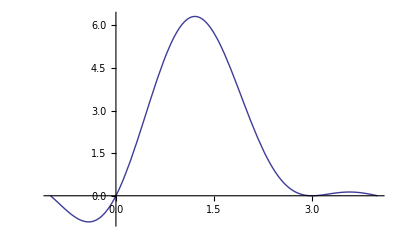

```mathematica
Plot[bb3[7,x],{x,-1,4}]
```

-Graphics-

```mathematica
FullSimplify[Sin[Pi z]/Pi  Sum[(-1)^k (x^(k-1)/(k-1)!)/(z-k),{k,1,Infinity}]]
```

(x^(-1+z) (Gamma[1-z]-Gamma[1-z,x]) Sin[π z])/π

```mathematica
Table[Limit[(x^(-1+z) (Gamma[1-z]-Gamma[1-z,x]) Sin[π z])/π,z->k],{k,0,5}]
```

{0,1,x,x^2/2,x^3/6,x^4/24}

```mathematica
Table[FullSimplify[(-1)^k Sin[Pi z]/Pi/(z-k)],{k,0,5}]
```

{Sin[π z]/(π z),Sin[π z]/(π-π z),Sin[π z]/(π (-2+z)),Sin[π z]/(3 π-π z),Sin[π z]/(π (-4+z)),Sin[π z]/(5 π-π z)}

```mathematica
Clear[z]
bbn[n_,z_]:=(Gamma[1+n] Gamma[1-z] Sin[π z])/(π z Gamma[1+n-z])
```

```mathematica
bbn[8,1/2]
```

65536/(6435 π)

```mathematica
Binomial[7.8,3.1]
```

53.3087

```mathematica
FullSimplify@Sin[Pi z]/Pi  Sum[(-1)^k Binomial[n,k]/(z-k),{k,0,Infinity}]
```

(Gamma[1+n] Gamma[1-z] Sin[π z])/(π z Gamma[1+n-z])

```mathematica
(Gamma[1+n] Gamma[1-z] Sin[π z])/(π z Gamma[1+n-z])/.n->7.8/.z->3.1
```

53.3087

```mathematica
FullSimplify[Sin[Pi z]/Pi  Sum[(-1)^k x^(k)/(k)!/(z-k),{k,0,Infinity}]]
```

((ExpIntegralE[1+z,x]-x^z Gamma[-z]) Sin[π z])/π

```mathematica
Table[Limit[((ExpIntegralE[1+z,x]-x^z Gamma[-z]) Sin[π z])/π,z->k],{k,0,6}]
```

{1,x,x^2/2,x^3/6,x^4/24,x^5/120,x^6/720}

```mathematica
FullSimplify[Sin[Pi z]/Pi  Sum[(-1)^k/(z-k) 1,{k,1,Infinity}]]
```

(HurwitzLerchPhi[-1,1,1-z] Sin[π z])/π

```mathematica
Table[Limit[(HurwitzLerchPhi[-1,1,1-z] Sin[π z])/π,z->k],{k,0,6}]
```

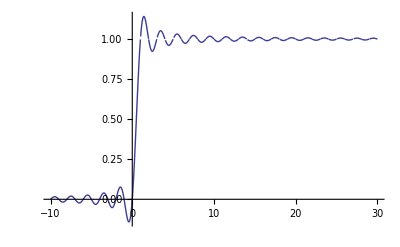

```mathematica
Plot[(HurwitzLerchPhi[-1,1,1-z] Sin[π z])/π,{z,-10,30}]
```

```mathematica
Sum[(-1)^k/(z-k) 1,{k,1,Infinity}]
```

HurwitzLerchPhi[-1,1,1-z]

```mathematica
FullSimplify[Sin[Pi z]/Pi  Sum[(-1)^k/(z-k) 1/k,{k,1,Infinity}]]
```

((HurwitzLerchPhi[-1,1,1-z]-Log[2]) Sin[π z])/(π z)

```mathematica
pp[x_,z_]:=Hypergeometric1F1[z,z+1,Log[x]] (Log[x]^z)/(z!)
```

```mathematica
FullSimplify[D[pp[x,z],z]/.z->0]
```

1/2 (Log[1/Log[x]]+Log[Log[x]])+LogIntegral[x]

```mathematica
Plot[bb3[997,zz]-bb3[996,zz],{zz,-2,6}]
```

```mathematica
FullSimplify@Sin[Pi z]/Pi  Sum[((-1)^k)/(z-k) x^k/k!,{k,0,Infinity}]
```

(x^z (Gamma[1-z]+z Gamma[-z,x]) Sin[π z])/(π z)

```mathematica
bz[x_,z_]:=((ExpIntegralE[1+z,x]-x^z Gamma[-z]) Sin[π z])/π
```

```mathematica
FullSimplify@bz[12,-3/2]
```

-1/(48 √(3 π))+ExpIntegralE[-1/2,12]/π

```mathematica
12^(-3/2)/((-3/2)!)
```

-1/(48 √(3 π))

```mathematica
FullSimplify@Sin[Pi z]/Pi  Sum[(-1)^k Binomial[n,k]/(z-k),{k,0,Infinity}]
```

(Gamma[1+n] Gamma[1-z] Sin[π z])/(π z Gamma[1+n-z])

```mathematica
brz[n_,z_]:=(Gamma[1+n] Gamma[1-z] Sin[π z])/(π z Gamma[1+n-z])
```

```mathematica
FullSimplify@brz[12,-3/2+I]
```

-(479001600 Cosh[π] Gamma[3/2-ⅈ])/(π Gamma[29/2-ⅈ])

```mathematica
Binomial[12,-3/2+I]
```

Binomial[12,-3/2+ⅈ]

```mathematica
FullSimplify@Sin[Pi z]/Pi  Sum[(-1)^k (x^(k-1)/(k-1)!)/(z-k),{k,0,Infinity}]
```

(x^(-1+z) (Gamma[1-z]-Gamma[1-z,x]) Sin[π z])/π

```mathematica
FullSimplify@Expand[(1/Gamma[z]/Gamma[1-z])  Sum[(-1)^k (x^(k)/(k)!)/(z-k),{k,0,Infinity}]]
```

x^z/Gamma[1+z]+(ExpIntegralE[1+z,x] Sin[π z])/π

```mathematica
FullSimplify@Expand[(1/Gamma[z]/Gamma[1-z])  Integrate[(-1)^k (x^(k)/(k)!)/(z-k),{k,0,Infinity}]]
```

((∫_0^∞ ((-1)^k x^k)/((-k+z) k!)ⅆk) Sin[π z])/π

```mathematica
FullSimplify[1/Gamma[z]/Gamma[1-z]]
```

Sin[π z]/π

```mathematica
Expand@(1/Gamma[z]/Gamma[1-z])  Sum[(-1)^k Binomial[n,k]/(z-k),{k,0,Infinity}]
```

Gamma[1+n]/(z Gamma[1+n-z] Gamma[z])

```mathematica
FullSimplify@Expand[(1/Gamma[z]/Gamma[1-z])  Sum[(-1)^k (Log[x]^(k-1)/(k-1)!)/(z-k),{k,1,Infinity}]]
```

((Gamma[1-z]-Gamma[1-z,Log[x]]) Log[x]^(-1+z) Sin[π z])/π

```mathematica
FullSimplify@Limit[((Gamma[1-z]-Gamma[1-z,Log[x]]) Log[x]^(-1+z) Sin[π z])/π,z->-1/2]
```

-(√π-2 Gamma[3/2,Log[x]])/(2 π Log[x]^(3/2))

```mathematica
FullSimplify@(Log[x]^(z-1))/(z-1)!/.z->-1/2
```

-1/(2 √π Log[x]^(3/2))

```mathematica
Clear[bb3a]
bb3[n_,z2_]:=Limit[Sin[Pi z]/Pi  Sum[(-1)^k d2[n,k]/(z-k),{k,1,Log2@n}],z->z2]
bb3a[n_,z_,k_]:=bb3a[n,z,k]=Sum[1/(z-k)-bb3a[Floor[n/j],z,k+1],{j,2,n}]
bb3az[n_,z_]:=-Sin[Pi z]/Pi bb3a[n,z,1]
bb3ax[n_,z_,k_,j_]:=If[n<j,0,1/(z-k)-bb3ax[n/j,z,k+1,2]+bb3ax[n,z,k,j+1]]
bb3ay[n_,z_]:=(-Sin[Pi z]/Pi) Expand@bb3ax[n,z,1,2]
FI[n_]:=FactorInteger[n];FI[1]:={}
sp[n_]:= Sum[p[[2]],{p,FI[n]}]
dbb3[n_,z_]:=dbb3[n,z]=FullSimplify[bb3[n,z]-bb3[n-1,z]]
dbb3a[n_,z_]:=FullSimplify[FullSimplify@dbb3[n,z]/(Sin[Pi z]/Pi) FactorialPower[z-1,sp[n]]]
```

```mathematica
Expand@bb3[100,z]
```

(7 Sin[π z])/(π (-6+z))-(51 Sin[π z])/(π (-5+z))+(184 Sin[π z])/(π (-4+z))-(324 Sin[π z])/(π (-3+z))+(283 Sin[π z])/(π (-2+z))-(99 Sin[π z])/(π (-1+z))

```mathematica
Expand@bb3az[100,z]
```

(7 Sin[π z])/(π (-6+z))-(51 Sin[π z])/(π (-5+z))+(184 Sin[π z])/(π (-4+z))-(324 Sin[π z])/(π (-3+z))+(283 Sin[π z])/(π (-2+z))-(99 Sin[π z])/(π (-1+z))

```mathematica
bb3ay[100,z]
```

-((-7/(-6+z)+51/(-5+z)-184/(-4+z)+324/(-3+z)-283/(-2+z)+99/(-1+z)) Sin[π z])/π

```mathematica
Table[dbb3a[2^n 3^2 ,z],{n,1,6}]
```

{-2 z,z (5+z),-6 z (3+z),12 z (7+3 z),-240 z (2+z),360 z (9+5 z)}

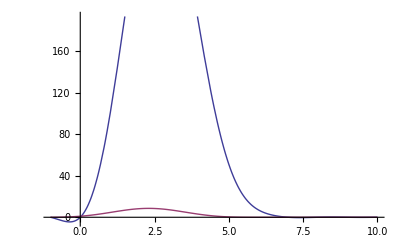

```mathematica
Plot[{bb3az[100,z],Binomial[Log[100],z]},{z,-1,10}]
```

```mathematica
FullSimplify@D[bb3az[100,z],z]
```

(7/(-6+z)-51/(-5+z)+184/(-4+z)-324/(-3+z)+283/(-2+z)-99/(-1+z)) Cos[π z]+((-7/(-6+z)^2+51/(-5+z)^2-184/(-4+z)^2+324/(-3+z)^2-283/(-2+z)^2+99/(-1+z)^2) Sin[π z])/π

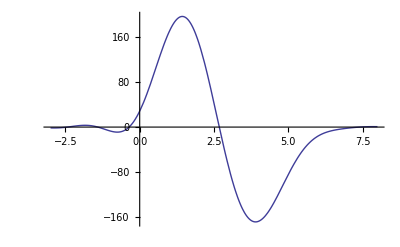

```mathematica
Plot[(7/(-6+z)-51/(-5+z)+184/(-4+z)-324/(-3+z)+283/(-2+z)-99/(-1+z)) Cos[π z]+((-7/(-6+z)^2+51/(-5+z)^2-184/(-4+z)^2+324/(-3+z)^2-283/(-2+z)^2+99/(-1+z)^2) Sin[π z])/π,{z,-3,8}]
```

```mathematica
FullSimplify@D[Binomial[Log[100],z],z]
```

Binomial[Log[100],z] (-HarmonicNumber[z]+HarmonicNumber[-z+Log[100]])

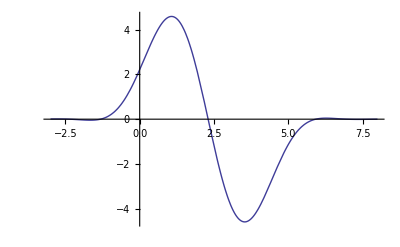

```mathematica
Plot[Binomial[Log[100],z] (-HarmonicNumber[z]+HarmonicNumber[-z+Log[100]]),{z,-3,8}]
```

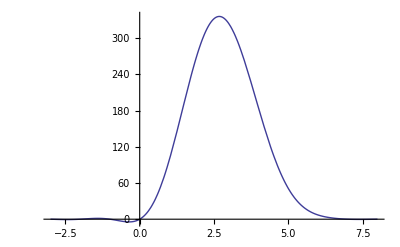

```mathematica
Plot[{bb3az[100,z]},{z,-3,8}]
```

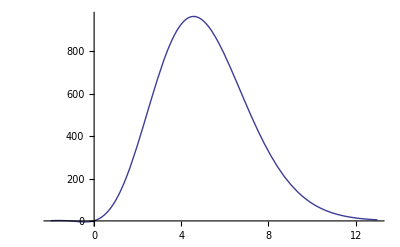

```mathematica
Plot[Hypergeometric1F1[z,z+1,Log[100]](Log[100]^z)/z!,{z,-2,13}]
```

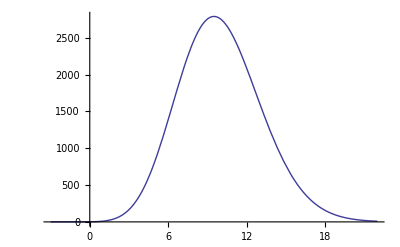

```mathematica
Plot[{10^z/z!},{z,-3,22}]
```

```mathematica
xr[x_,z_]:=x^z/z!
```

```mathematica
xr[10,10]/xr[10,11]
```

11/10

```mathematica
FullSimplify[D[10^z/(z!),z]]
```

(10^z (EulerGamma-HarmonicNumber[z]+Log[10]))/Gamma[1+z]

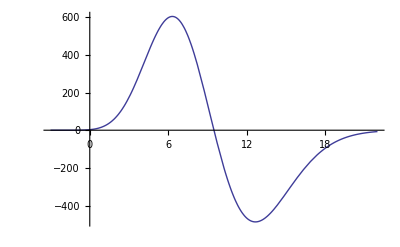

```mathematica
Plot[{(10^z (EulerGamma-HarmonicNumber[z]+Log[10]))/Gamma[1+z]},{z,-3,22}]
```

```mathematica
Plot[bb3az[100,z],{z,-3,8}]
```

-Graphics-

```mathematica
D[bb3az[100,z],z]
```

```mathematica
Plot[bb3az[100,z],{z,6.9,7.1}]
```

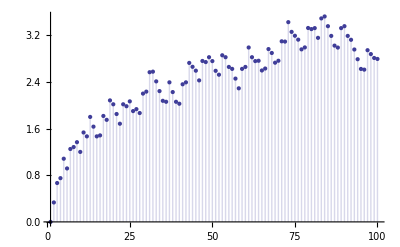

```mathematica
DiscretePlot[D[bb3az[n,z],z]/.z->-2,{n,1,100}]
```

```mathematica
Floor[Log2@100]
```

6

```mathematica
pp[n_,k_]:=pp[n,k]=Sum[1/k-pp[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
DiscretePlot[pp[n,3],{n,1,100}]
```

-Graphics-

```mathematica
binomial[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
FI[n_]:=FactorInteger[n];FI[1]:={}
dz[n_,z_]:=Product[(-1)^p[[2]] binomial[-z,p[[2]]],{p,FI[n]}]
Ddz[n_,z_]:=Sum[dz[j,z],{j,1,n}]
```

```mathematica
FullSimplify[Sum[dbb3[j,z]dbb3[210/j,y],{j,Divisors[210]}]]
```

(2 (12 z (1+z)+y (12+(7-17 z) z)+y^2 (12+z (-17+7 z))) Sin[π y] Sin[π z])/(π^2 (-3+y) (-2+y) (-1+y) (-3+z) (-2+z) (-1+z))

```mathematica
dbb3[210,4]
```

24

```mathematica
Limit[Limit[(2 (12 z (1+z)+y (12+(7-17 z) z)+y^2 (12+z (-17+7 z))) Sin[π y] Sin[π z])/(π^2 (-3+y) (-2+y) (-1+y) (-3+z) (-2+z) (-1+z)),y->-1],z->5]
```

0

```mathematica
Sum[Binomial[a,z]Binomial[10-a,y],{a,0,10}]
```

Binomial[5,y] Binomial[5,z]+Binomial[4,z] Binomial[6,y]+Binomial[4,y] Binomial[6,z]+Binomial[3,z] Binomial[7,y]+Binomial[3,y] Binomial[7,z]+Binomial[2,z] Binomial[8,y]+Binomial[2,y] Binomial[8,z]+Binomial[1,z] Binomial[9,y]+Binomial[1,y] Binomial[9,z]+Binomial[0,z] Binomial[10,y]+Binomial[0,y] Binomial[10,z]

```mathematica
Clear[br3a]
br3a[n_,z_,k_]:=br3a[n,z,k]=Sum[(-1)^(j+1)(1/(z-k)-br3a[Floor[n/j],z,k+1]),{j,2,n}]
br3az[n_,z_]:=-Sin[Pi z]/Pi br3a[n,z,1]
```

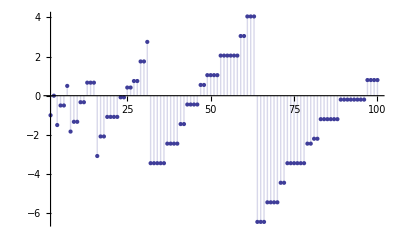

```mathematica
DiscretePlot[D[br3az[n,z],z]/.z->0,{n,2,100}]
```